```mathematica
f11[x1_,x2_]:=Cos[x1]Cos[x2]
```

```mathematica
f21[x1_,x2_]:=Sin[x1]
```

```mathematica
f31[x1_,x2_]:=Cos[x1]Sin[x2]
```

```mathematica
df111[x1_,x2_]:=D[f11[z1,z2],z1]/.{z1->x1,z2->x2}
```

```mathematica
df112[x1_,x2_]:=D[f11[z1,z2],z2]/.{z1->x1,z2->x2}
```

```mathematica
df211[x1_,x2_]:=D[f21[z1,z2],z1]/.{z1->x1,z2->x2}
```

```mathematica
df212[x1_,x2_]:=D[f21[z1,z2],z2]/.{z1->x1,z2->x2}
```

```mathematica
df311[x1_,x2_]:=D[f31[z1,z2],z1]/.{z1->x1,z2->x2}
```

```mathematica
df312[x1_,x2_]:=D[f31[z1,z2],z2]/.{z1->x1,z2->x2}
```

```mathematica
Show[Plot3D[{Max[Abs[f11[x,y]],Abs[f21[x,y]],Abs[f31[x,y]]]},{x,0,Pi/2},{y,0,Pi/2},PlotPoints->50,Exclusions->None,MaxRecursion->3,Mesh->None],ContourPlot3D[-Sqrt[2]x+2y==0,{x,0,Pi/2},{y,0,Pi/2},{z,0.5,1.0},Mesh->None,ContourStyle->LightBlue]]
```

-Graphics3D-

```mathematica
r=FindRoot[Tan[x1]-Cos[Sqrt[2]/2 x1],{x1,0}]
```

{x1→0.718156}

```mathematica
x1=x1/.r
```

0.718156

```mathematica
x2=Sqrt[2]/2 x1
```

0.507813

```mathematica
Show[ContourPlot[{Max[Abs[f11[x,y]],Abs[f21[x,y]],Abs[f31[x,y]]]},{x,0,Pi/2},{y,0,Pi/2},Contours->25,PlotPoints->50,Exclusions->None],ContourPlot[Sqrt[2]x-2y==0,{x,0,Pi/2},{y,0,Pi/2},ContourStyle->Cyan],ContourPlot[{If[Abs[f11[x,y]]>Abs[f31[x,y]],Abs[f11[x,y]]-Abs[f21[x,y]]],If[Abs[f21[x,y]]>Abs[f11[x,y]],Abs[f21[x,y]]-Abs[f31[x,y]]],If[Abs[f31[x,y]]>Abs[f21[x,y]],Abs[f31[x,y]]-Abs[f11[x,y]]]},{x,0,Pi/2},{y,0,Pi/2},Contours->{0.0},ContourStyle->{{Red,Thick},{Green,Thick},{Blue,Thick}},ContourShading->None],Graphics[{PointSize[Large],Black,Point[{x1,x2}]}],Graphics[{Thick,White,Arrow[{{x1,x2},{x1+(df112[x1,x2]-df212[x1,x2])/3,x2+(-df111[x1,x2]+df211[x1,x2])/3}}]}]]
```

-Graphics-

```mathematica
g[x_,y_]:=Grad[Max[Abs[f11[x,y]],Abs[f21[x,y]],Abs[f31[x,y]]],{x,y}]
```

```mathematica
g[x,y][[1]]
```

Piecewise[{{-Cos[y] Sin[x] Abs'[Cos[x] Cos[y]], Abs[Cos[x] Cos[y]]-Abs[Sin[x]]≥0&&Abs[Cos[x] Cos[y]]-Abs[Cos[x] Sin[y]]≥0}, {Cos[x] Abs'[Sin[x]], Abs[Cos[x] Cos[y]]-Abs[Sin[x]]<0&&Abs[Sin[x]]-Abs[Cos[x] Sin[y]]≥0}, {-Sin[x] Sin[y] Abs'[Cos[x] Sin[y]], True}}]

```mathematica
g[x,y][[2]]
```

Piecewise[{{-Cos[x] Sin[y] Abs'[Cos[x] Cos[y]], Abs[Cos[x] Cos[y]]-Abs[Sin[x]]≥0&&Abs[Cos[x] Cos[y]]-Abs[Cos[x] Sin[y]]≥0}, {0, Abs[Cos[x] Cos[y]]-Abs[Sin[x]]<0&&Abs[Sin[x]]-Abs[Cos[x] Sin[y]]≥0}, {Cos[x] Cos[y] Abs'[Cos[x] Sin[y]], True}}]

```mathematica
Show[ContourPlot[{Max[Abs[f11[x,y]],Abs[f21[x,y]],Abs[f31[x,y]]]},{x,0,Pi},{y,0,Pi},Contours->28,PlotPoints->50,Exclusions->None],ParametricPlot[{Mod[t,Pi],Mod[Sqrt[2]/2 t,Pi]},{t,0,41Pi-1/1000},PlotStyle->Black]]
```

-Graphics-

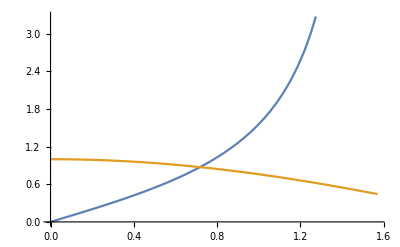

```mathematica
Plot[{Tan[x1],Cos[Sqrt[2]/2 x1]},{x1,0,Pi/2}]
```

```mathematica
Solve[Tan[x1]-Cos[Sqrt[2]/2 x1]==0,x1]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-Cos[x1/(√2)]+Tan[x1]==0,x1]

```mathematica
NSolve[Tan[x1]-Cos[Sqrt[2]/2 x1]==0,x1]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[-Cos[x1/(√2)]+Tan[x1]==0,x1]

```mathematica
r=FindRoot[Tan[x1]-Cos[Sqrt[2]/2 x1],{x1,0}]
```

{x1→0.718156}

```mathematica
Sqrt[2]/2 x1/.r
```

0.507813

```mathematica
Cos[x1/.r]Cos[Sqrt[2]/2 x1/.r]
```

0.657997

```mathematica
Sin[x1/.r]
```

0.657997